# Zadanie 1

-1/2+2 ⅇ^-x x^2

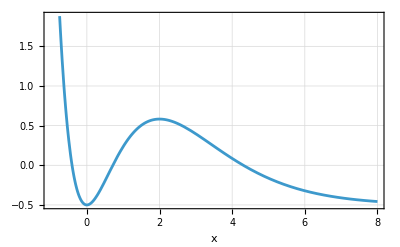

```mathematica
f[x_]=-1/2+2 x^2 ⅇ^-x
wykres=Plot[f[x],{x,-1,8},AxesLabel->Automatic,GridLines->Automatic,Frame->True]
```

```mathematica
sol= {x,0}/.NSolve[f[x]==0,x,Reals]
```

{{-0.407777,0},{0.714806,0},{4.30658,0}}

```mathematica
extr= {x,f[x]}/.Solve[D[f[x],x]==0,x,Reals]
```

{{0,-1/2},{2,-1/2+8/ⅇ^2}}

{{0.,0},{2. Null,0}}

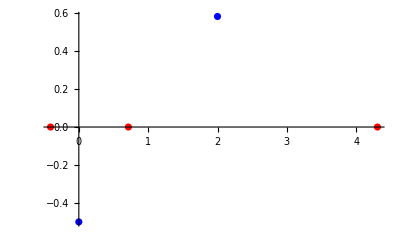

```mathematica
pkt=ListPlot[{sol,extr},PlotStyle->{{Red,Large},{Blue,Large}}]
```

```mathematica
Limit[f[x],x->∞]
```

ReplaceAll::reps: {-1/2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0,-1/2+2 ⅇ^-x x^2}/.-1/2

```mathematica
as=Limit[f[x],x->∞]
```

-1/2

Plot::optx: Unknown option Style→Dashing[{Small,Small}] in Plot[as,{x,-∞,∞},Style→Dashed].

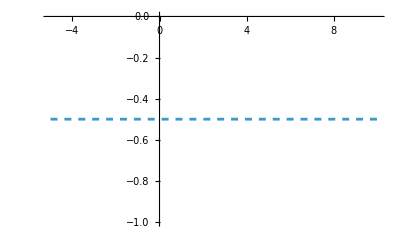

```mathematica
asy=Plot[as,{x,-5,10},PlotStyle->Dashed]
```

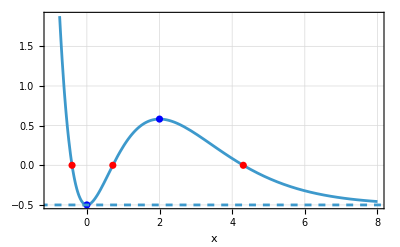

```mathematica
Show[wykres,pkt,asy]
```

# Zad

4 x-x^2

0.5 x

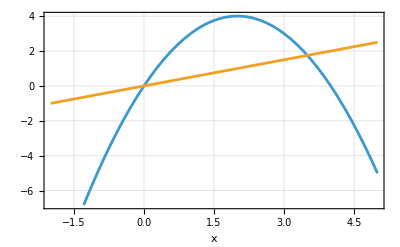

{{0.,0.},{3.5,1.75}}

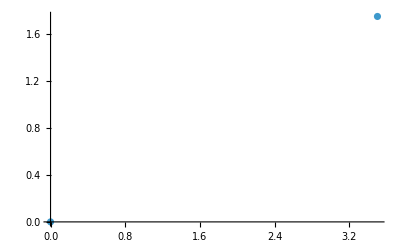

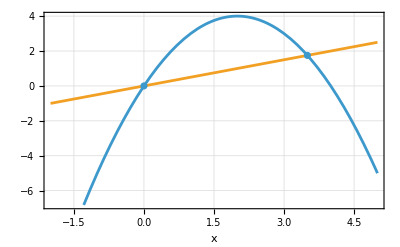

```mathematica
y1[x_]=-x^2+4x
y2[x_]=0.5 x

w1=Plot[{y1[x],y2[x]},{x,-2,5},GridLines->Automatic,Frame->True,AxesLabel->Automatic]
pkt={x,y1[x]}/.Solve[y1[x]==y2[x],x]
w2=ListPlot[pkt]
w3={x,y1[x]}
Show[w1,w2,w3]
```